```mathematica
KALIBRACJA WYDAJNOSCI
```

KALIBRACJA WYDAJNOSCI

```mathematica
VTb=0.0000193; (*objętość molowa*)
VCo=0.00000667;
VGd=0.000019903; 
VFe=0.00000709;
VRE = VTb; (*wybranie pierwiastka RE*)
VTM = VCo ;(*wybranie pierwiastka TM*)
VTM2 = VFe; (*wybranie drugiego pierwiastka TM*)
LiczbaPierwiastkow = 2 ; (*2 lub 3 pierwiastki dla 3 zakładamy stop TM12.5Fe87.5*)
ro=65;(* wartość ro dla której znajdujemy sie w pozycji 0,0 na podlozu*)
De=147; (*wysokosc target-podloze*)
pierscien=1; (*1- target pierscieniowy; 0 - target pelny*)
If[LiczbaPierwiastkow==2,
{
cRE=100*(tRE/VRE)/((tRE/VRE)+(tTM/VTM)); (*wzor na stezenie*)
t=tTM+tRE; (*wzor na calkowita grubosc*)
Z=Solve[cRE==22&&t==300,{tRE,tTM},Reals]//N; (*tutaj mozemy podac stezenie i docelowa grubosc na srodku podlozu*)
GruboscRE=Z[[1,1,2]];
GruboscTM=Z[[1,2,2]];
GruboscTM2 = 0;
},
{
cTM=12.5;
cRE=100*(tRE/VRE)/((tRE/VRE)+(tTM/VTM)+(tTM2/VTM2)); (*wzor na stezenie*)
tTM2=tTM((100-cTM) VTM2)/(cTM VTM);
t=tTM2+tTM+tRE; (*wzor na calkowita grubosc*)
Z=Solve[cRE==21.3&&t==300,{tRE,tTM},Reals]//N; (*tutaj mozemy podac stezenie i docelowa grubosc na srodku podlozu*)
GruboscRE=Z[[1,1,2]];
GruboscTM=Z[[1,2,2]];
GruboscTM2=Z[[1,2,2]]*((100-cTM) VTM2)/(cTM VTM);
}
];

If[De == 97,
	{If[pierscien==0,G=0.05039637727499997,G=0.024174414662499893]},
{
If[De ==147,
    {If[pierscien==0,G=0.04669458558124996,G=0.02524742172499997]},
{
If[De==177,
If[pierscien==0,G=0.0387347059,G=0.0213398759]
]}]
}];
G
wydajnoscRE=GruboscRE/G
wydajnoscTM=GruboscTM/G
wydajnoscTM2=GruboscTM2/G
Grubosc3=GruboscRE+GruboscTM
stezenie=100*((GruboscRE/VRE)/((GruboscRE/VRE)+(GruboscTM/VTM)))
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.0252474

5339.7

6542.7

0.

300.

22.

```mathematica
(*(środek w (0,0,De), xszer= x szerokość, yszer= y szerokość) z dawki z okrągłego targetu o promieniu R, którego środek jest położony w (xt,yt,0)
nx, ny - ilość punktów wzdłuż x i y w mapie
Promien targetu i kominka R=25mm; wysokość kominka Y=30mm, aby te parametry zmienić należy przeliczyć numerycznie
Ostateczne grubosci podawane są w A*)
```

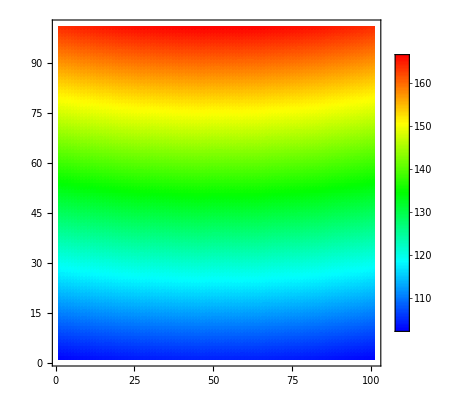

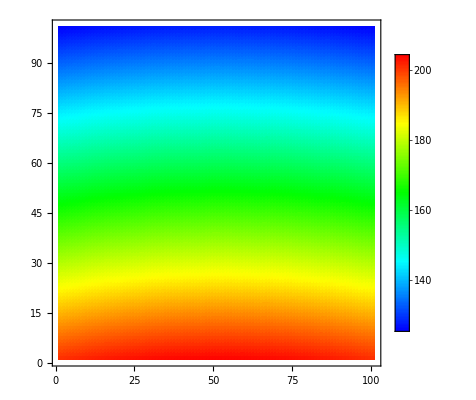

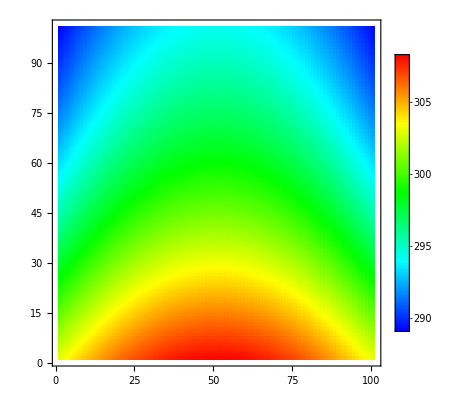

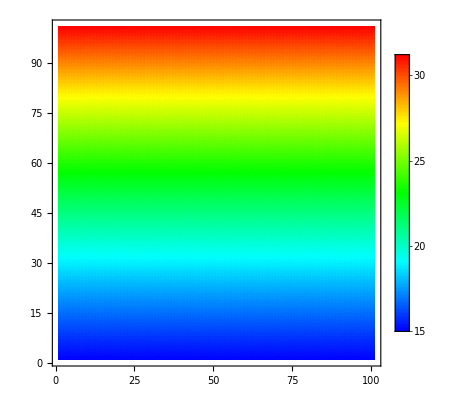

```mathematica
nx=101;
ny=101;
xt=65;
yt=0;
xt2=-65;
yt2=0;
xszer=20;
yszer=20;
GruboscRE=Table[0,{i,1,nx},{j,1,ny}];
GruboscTM=Table[0,{i,1,nx},{j,1,ny}];
GruboscTM2=Table[0,{i,1,nx},{j,1,ny}];
GruboscTMTM2=Table[0,{i,1,nx},{j,1,ny}];
GruboscRETM=Table[0,{i,1,nx},{j,1,ny}];
GruboscRETMTM2=Table[0,{i,1,nx},{j,1,ny}];
stezenieRE=Table[0,{i,1,nx},{j,1,ny}];
stezenieTM=Table[0,{i,1,nx},{j,1,ny}];
stezenieTM2=Table[0,{i,1,nx},{j,1,ny}];
stezenieTMTM2=Table[0,{i,1,nx},{j,1,ny}];
dx=xszer/(nx-1);
dy=yszer/(ny-1);

For[i2=0,i2<ny,i2++,  (*petla po y*)
For[i1=0,i1<nx,i1++,  (*petla po x*)
ro=Sqrt[(-0.5*xszer+i1*dx-xt)^2+(-0.5*yszer+i2*dy-yt)^2];
ro2=Sqrt[(-0.5*xszer+i1*dx-xt2)^2+(-0.5*yszer+i2*dy-yt2)^2];
If[De==97,
{
If[pierscien==0,
{
GRE=0.30694-Sign[ro]*0.00462*ro-(1.80316*10^(-5))*ro^2+Sign[ro]*(6.0995*10^(-7))*ro^3-(2.66476*10^(-9))*ro^4;
GTM=0.30694-Sign[ro2]*0.00462*ro2-(1.80316*10^(-5))*ro2^2+Sign[ro2]*(6.0995*10^(-7))*ro2^3-(2.66476*10^(-9))*ro2^4;
},
{
GRE=0.1605-Sign[ro]*(7.86875*10^(-4))*ro-(7.60412*10^(-5))*ro^2+Sign[ro]*(1.18874*10^(-6))*ro^3-(5.06214*10^(-9))*ro^4;
GTM=0.1605-Sign[ro2]*(7.86875*10^(-4))*ro2-(7.60412*10^(-5))*ro2^2+Sign[ro2]*(1.18874*10^(-6))*ro2^3-(5.06214*10^(-9))*ro2^4;
}]
},
If[De==147,
{
If[pierscien==0,
{
GRE=0.08882+Sign[ro]*(5.35115*10^(-4))*ro-(3.69132*10^(-5))*ro^2+Sign[ro]*(3.62707*10^(-7))*ro^3-(1.15167*10^(-9))*ro^4;
GTM=0.08882+Sign[ro2]*(5.35115*10^(-4))*ro2-(3.69132*10^(-5))*ro2^2+Sign[ro2]*(3.62707*10^(-7))*ro2^3-(1.15167*10^(-9))*ro2^4;
},
{
GRE=-0.01614+Sign[ro]*(0.0038)*ro-(8.74652*10^(-5))*ro^2+Sign[ro]*(7.38735*10^(-7))*ro^3-(2.18184*10^(-9))*ro^4;
GTM=-0.01614+Sign[ro2]*(0.0038)*ro2-(8.74652*10^(-5))*ro2^2+Sign[ro2]*(7.38735*10^(-7))*ro2^3-(2.18184*10^(-9))*ro2^4;
}]
},
If[De==177,
{
If[pierscien==0,
{
GRE=0.06095+Sign[ro]*(2.90768*10^(-4))*ro-(1.80091*10^(-5))*ro^2+Sign[ro]*(1.56591*10^(-7))*ro^3-(4.49578*10^(-10))*ro^4;
GTM=0.06095+Sign[ro2]*(2.90768*10^(-4))*ro2-(1.80091*10^(-5))*ro2^2+Sign[ro2]*(1.56591*10^(-7))*ro2^3-(4.49578*10^(-10))*ro2^4;
},
{
GRE=-0.00818+Sign[ro]*(0.00225)*ro-(4.77588*10^(-5))*ro^2+Sign[ro]*(3.82178*10^(-7))*ro^3-(1.10855*10^(-9))*ro^4;
GTM=-0.00818+Sign[ro2]*(0.00225)*ro2-(4.77588*10^(-5))*ro2^2+Sign[ro2]*(3.82178*10^(-7))*ro2^3-(1.10855*10^(-9))*ro2^4;
}]
}]
]
];

GruboscRE[[i1+1,i2+1]]=wydajnoscRE*GRE//N;
GruboscTM[[i1+1,i2+1]]=wydajnoscTM*GTM//N;
GruboscTM2[[i1+1,i2+1]]=wydajnoscTM2*GTM//N; (*GTM i GTM2 posiadają te same wartosci*)
GruboscRETM[[i1+1,i2+1]]=GruboscTM[[i1+1,i2+1]]+GruboscRE[[i1+1,i2+1]]//N;
GruboscRETMTM2[[i1+1,i2+1]]=GruboscRE[[i1+1,i2+1]]+GruboscTM[[i1+1,i2+1]]+GruboscTM2[[i1+1,i2+1]]//N;
stezenieRE[[i1+1,i2+1]]=100*((GruboscRE[[i1+1,i2+1]]/VRE)/((GruboscRE[[i1+1,i2+1]]/VRE)+(GruboscTM[[i1+1,i2+1]]/VTM)+(GruboscTM2[[i1+1,i2+1]]/VTM2)))//N;
stezenieTM[[i1+1,i2+1]]=100*((GruboscTM[[i1+1,i2+1]]/VTM)/((GruboscRE[[i1+1,i2+1]]/VRE)+(GruboscTM[[i1+1,i2+1]]/VTM)+(GruboscTM2[[i1+1,i2+1]]/VTM2)))//N;
stezenieTM2[[i1+1,i2+1]]=100*((GruboscTM2[[i1+1,i2+1]]/VTM2)/((GruboscRE[[i1+1,i2+1]]/VRE)+(GruboscTM[[i1+1,i2+1]]/VTM)+(GruboscTM2[[i1+1,i2+1]]/VTM2)))//N;
stezenieTMTM2[[i1+1,i2+1]]=100*((GruboscTM2[[i1+1,i2+1]]/VTM2)/((GruboscTM[[i1+1,i2+1]]/VTM)+(GruboscTM2[[i1+1,i2+1]]/VTM2)))//N;
]
];
ListDensityPlot[GruboscRE,ImageSize->400, ColorFunction->(Hue[2 (1-#1)/3]&),PlotLegends->Automatic]
ListDensityPlot[GruboscTM,ImageSize->400, ColorFunction->(Hue[2 (1-#1)/3]&),PlotLegends->Automatic]
ListDensityPlot[GruboscRETM,ImageSize->400, ColorFunction->(Hue[2 (1-#1)/3]&),PlotLegends->Automatic]
ListDensityPlot[stezenieRE,ImageSize->400, ColorFunction->(Hue[2 (1-#1)/3]&),PlotLegends->Automatic]
```

```mathematica
stezenieRE[[51,51]]
GruboscRETM[[51,51]]
stezenie[[100,50]]-stezenie[[1,50]];
stezenie[[1,50]];
stezenie[[100,50]];
```

22.

300.

Part::partd: Part specification 22.⟦100,50⟧ is longer than depth of object.

Part::partd: Part specification 22.⟦1,50⟧ is longer than depth of object.

Part::partd: Part specification 22.⟦100,50⟧ is longer than depth of object.

```mathematica
Export["gruboscRETM.xls",GruboscRETM,"Table"]
```

gruboscRETM.xls